# Higgs to distop decay 2

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/bdcd/0.m, 1 diagram

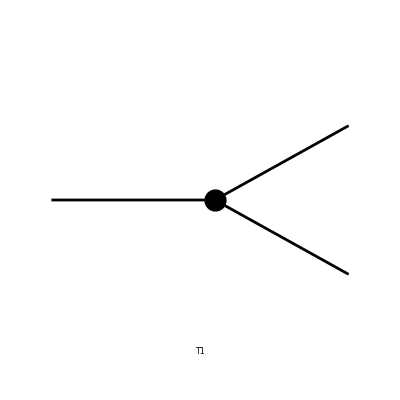

```mathematica
topo1=CreateTopologies[0,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 94 particles (incl. antiparticles) in 23 classes

> $CounterTerms are ON

> 383 vertices

classes model {MSSM} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/bdcd/0.m, 1 diagram

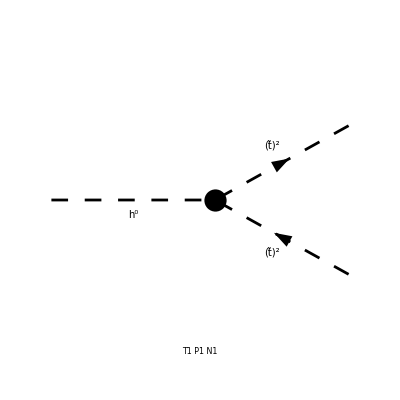

```mathematica
diag1=InsertFields[topo1,{S[1]}->{S[13,{2,3}],-S[13,{2,3}]},InsertionLevel->{Particles},Model->"MSSM"];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag1],FermionChains->Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],Mh0,{}}}→{{S[13,{2,3,Col2}],k[2],MSf[2,3,3],{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-S[13,{2,3,Col3}],k[3],MSf[2,3,3],{-(2 Charge)/3,-(2 ColorCharge)/(√3)}}}][-(EL Sub5 Mat[SUN1])/(6 CW MW SB SW)]

#### Check divergent piece

```mathematica
UVDivergentPart[amp]
divergence=%[[1]]
```

Amp[{{S[1],k[1],Mh0,{}}}→{{S[13,{2,3,Col2}],k[2],MSf[2,3,3],{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-S[13,{2,3,Col3}],k[3],MSf[2,3,3],{-(2 Charge)/3,-(2 ColorCharge)/(√3)}}}][0]

0

#### Prepare for simplification

Note: polarization sum auto squares the matrix element

```mathematica
mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify
```

HelicityME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-4.frm

running FORM...

ok

1/(3 CW2 MW2 SB2 SW2)Alfa π (3 CW MT SA (MUEC USf[2,2,3,3] USfC[2,1,3,3]+MUE USf[2,1,3,3] USfC[2,2,3,3])+3 CA CW (2 MT2 USf[2,1,3,3] USfC[2,1,3,3]+MT Af[3,3,3] USf[2,2,3,3] USfC[2,1,3,3]+MT AfC[3,3,3] USf[2,1,3,3] USfC[2,2,3,3]+2 MT2 USf[2,2,3,3] USfC[2,2,3,3])+MW MZ SAB SB ((-3+4 SW2) USf[2,1,3,3] USfC[2,1,3,3]-4 SW2 USf[2,2,3,3] USfC[2,2,3,3]))^2

## Numerical Evaluation

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.23,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,MUEC -> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt)+MUE*Cot[β]),AfC[3,3,3]-> ((xt)+MUE*Cot[β]),AfC[3,3,3]->Af[3,3,3],
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->-Sin[thetat],USf[2,2,3,3]->Cos[thetat] ,USf[2,1,3,3]->Sin[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=mat//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

```mathematica
MyMatrixElement[500,1000,5,250,-0.1008,1.47]
```

162927.

```mathematica
Expand[%]
```

162927.

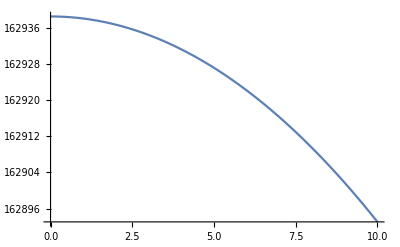

```mathematica
Plot[{MyMatrixElement[500,1000,xt,250,-0.1008,1.47]},{xt,0,10}]
```

## Higgs to distop

```mathematica
matrixEl = ghSS
```

ghSS

## Coupling definitions

Explicitly, we can write out these couplings in terms of MSSM parameters - for more details see my summary Latex document.

#### Z couplings

```mathematica
z11=-(e/(2*sW*cW))*(ct^2 - 4sW^2/3)
```

-(e (ct^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z22=-(e/(2*sW*cW))*(st^2 - 4sW^2/3)
```

-(e (st^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z12=(e/(2*sW*cW))*(ct*st)
```

(ct e st)/(2 cW sW)

Within these expressions, e is the elementary charge, s_W and c_W are the sine and cosine of the Weinberg angle, and c_t is the cosine of the stop mixing angle.

#### Z-γ couplings

```mathematica
zg11=(2e^2/(3*sW*cW))*(ct^2 - 4sW^2/3)
```

(2 e^2 (ct^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg22=(2e^2/(3*sW*cW))*(st^2 - 4sW^2/3)
```

(2 e^2 (st^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg12=-(2e^2/(3*sW*cW))*(ct*st)
```

-(2 ct e^2 st)/(3 cW sW)

#### Higgs couplings

```mathematica
h11= a*ct^2 +b*st^2 +2*c*ct*st
```

a ct^2-2 c ct st+b st^2

```mathematica
h22 = a*st^2 +b*ct^2 -2*c*ct*st
```

b ct^2-2 c ct st+a st^2

```mathematica
h12= -a*ct*st +b*ct*st +c*(ct^2-st^2)
```

-a ct st+b ct st+c (ct^2-st^2)

Where we have (in the decoupling limit)

```mathematica
a=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](1/2 -2*sW^2/3)
```

-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW)

```mathematica
b=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](2*sW^2/3)
```

-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW)

```mathematica
c = ((e*mt)/(2*mW*sW))(At-μ*Cot[β])
```

(e mt (At-μ Cot[β]))/(2 mW sW)

μ and β  are your standard MSSM paramters, m_t is the mass of the top, and A_t is a soft breaking term that can be expressed in terms of the stop mixing parameter and μ.

## Plug in values and compare to FeynArts result

```mathematica
matToSub =matrixEl//. ghSS-> h22
```

ct^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+st^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))-(ct e mt st (At-μ Cot[β]))/(mW sW)

```mathematica
SUBIN[stopMass1_,stopMass2_,xt_,mu_,beta_]:={
mt->173,
mW->80.4,
mZ-> 91.2,
mh-> 125,
Alfa->1/128,Alfa2->(1/128)^2,
sW->0.4796,cW-> (mW/mZ),
β-> beta,μ-> mu,
thetat-> (1/2)(ArcSin[(-2*mt*xt)/(stopMass2^2-stopMass1^2)]),
e-> Sqrt[(4*Pi*Alfa)],
m1->stopMass1,m2-> stopMass2,
At-> ((xt)+μ*Cot[β]),
ct->Cos[thetat] ,st->Sin[thetat]}
MyResults[stopMass1_,stopMass2_,xt_,mu_,beta_]:=matToSub//.SUBIN[stopMass1,stopMass2,xt,mu,beta]//Simplify
```

```mathematica
MyResults[250,1000,5,250,1.47]
```

-233.036

```mathematica
%^2
```

54305.7

```mathematica
%*3
```

162917.

```mathematica
Expand[%]
```

162917.

```mathematica
(3*(MyResults[250,1000,0,250,1.47])^2)/MyMatrixElement[250,1000,0,250,-0.1008,1.47]
```

0.999924

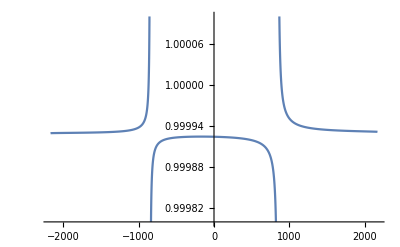

```mathematica
Plot[(3*(MyResults[500,1000,s,250,1.47])^2)/MyMatrixElement[500,1000,s,250,-0.1008,1.47],{s,-2167,2167},PlotRange->{0.9998,1.0001}]
```

```mathematica
t1 = 250
t2 = 500
```

```mathematica
Plot[(3*(MyResults[t1,t2,s,250,1.47])^2)/MyMatrixElement[t1,t2,s,250,-0.1008,1.47],{s,(t1^2-t2^2)/(346),(-t1^2+t2^2)/(346)}]
```